```mathematica
(* We want to consider the "classical" noise source, i.e. temperature fluctuation at core inlet plus an additional noise source from fuel assembly gap variations. 
*)
(* reference [1]: Pazsit: investogation of thr space-dependent noise induced by propagating perturbations, Ann.Nucl.En. 37 (2010) *)
(* we take formula (16) from [1]; G0 is the point reactor transfer function and rho is the induced reactivity change *)


deltaP[w_]:=G0[w]*rho[w];

(* in the frequency range of interest we assume G0 approximately constant: *)

G0[w_]:=1/beta;
beta=0.002;

(* the reactivity change is written as follows from (18) in [1] *)

H=3.90; (* core height *)
phi[z_]:=1; (* approximately flat flux along axial direction *)
nu=2.5;
Sf=0.0014;
C0=1/(nu*Sf);
v=4.0; (* speed 4m/s *)

rho[w_]:=C0*Integrate[phi[z]*phi[z]*deltaSa[z,w],{z,0,H}];

deltaSa[z_,w_]:=f1[w]+f2[z,w];

(* f1 is the reactivity perturbation from a z-independent source like from the gap variation *)
(* if f1 is white noise this means that f1 is constant *)

f1[w_]:=a1;

(* f2 is the perturbation which comes from the traveling reactivity perturbation introduced at core inlet *)
(* if the core inlet perturbation is white noise, then it follows: *)

f2[z_,w_]:=a2*Exp[-ⅈ*w*z/v];

a1=1;
a2=1;

PSD[w_]:=rho[w]*Conjugate[rho[w]]; (* proxy for power spectral density *)
```

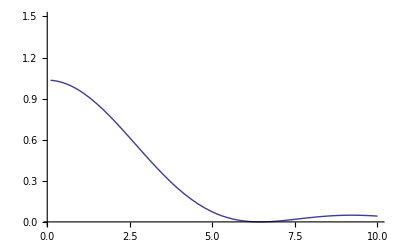

```mathematica
a1=0; (* no noise from fuel assembly gaps *)
Plot[PSD[w]/(1.2*10^6),{w,0.1,10},PlotRange->{0,1.5}]
```

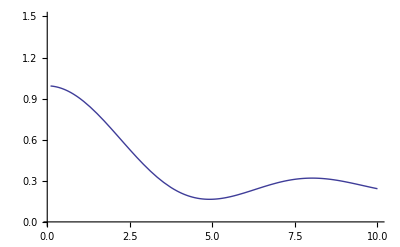

```mathematica
a1=1;
a2=1; (*  noise from both fuel assembly gaps and inlet T variation *)
Plot[PSD[w]/(5*10^6),{w,0.1,10},PlotRange->{0,1.5}]
```